# Homework 9

## Problem 9.1

A small bar of soap with mass m = 125 g is placed in a bowl of hemispherical shape. The soap can slide without friction on the surface of the bowl. The radius of curvature of the bowl is R=50.0 cm. Use a coordinate system where the z axis points upward. (Thus, when the soap is in the bottom of the bowl theta  = Pi .) The soap has no component of velocity in the phi (azimuthal) direction; that is, it slides only “up” and “down” the bowl, i.e. in the theta direction. Let the bar of soap be initially at an angle of  theta = 5*Pi / 6 (30 degrees up from the bottom of the bowl), and be moving up the bowl with a velocity of 2.00 m/s.

```mathematica
Clear["`*"]
```

```mathematica
g=9.8;
m=0.125;
R=0.5;
vtheta0=2;
theta0=5*Pi/6;
```

## Part A

Write down T as a function of vtheta and U as a function of theta. Take the zero value for U to be at the bottom of the bowl.

```mathematica
T[vtheta_]=m/2 * vtheta^2;
U[theta_]=m*g*R(1 +Cos[theta]);
```

### Solution

```mathematica
T$[vtheta_]=m/2*vtheta^2;
U$[theta_]=m*g*R*(1+Cos[theta]);
If[FullSimplify[Solve[T[a$]==T$[a$],a$]]=={{}},Print["T is correct."],Print["T is incorrect."]]
If[FullSimplify[Solve[U[a$]==U$[a$],a$]]=={{}},Print["U is correct."],Print["U is incorrect."]]
```

T is correct.

U is correct.

## Part B

Find the theta values in degrees that correspond to the classical turning points of the system. Call th1 the smaller and th2 the larger of the two.

Note that there are two solutions given by Mathematica. One is positive and one is negative. In our system, we have no negative angles, so you will need to change the negative solution to an equivalent angle between 0 and 2Pi.

```mathematica
E0= U[theta0] + T[vtheta0];
sol=Solve[U[theta]==E0,theta];
th2=theta/.sol[[1]];
th2 = th2 *180/Pi+360
th1 = theta/.sol[[2]] ;
th1 = th1 * 180 / Pi
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

242.751

117.249

### Solutions

```mathematica
th1$=117.2492410;
err1$=Abs[th1-th1$]/th1$;
th2$=242.7507590;
err2$=Abs[th2-th2$]/th2$;
If[err1$<.01,Print["th1 is correct."],Print["th1 is incorrect."]]
If [err2$<.01 ,Print["th2 is correct."],Print["th2 is incorrect."]]
```

th1 is correct.

th2 is correct.

#### Equations that can be used to solve for the angles

```mathematica
E0=U[theta0]+T[vtheta0];
sol=Solve[U[theta]==E0,theta];
th1=180/Pi*theta/.sol[[2]]
th2=360+180/Pi*theta/.sol[[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

117.249

242.751

## Part C

Plot U and E on the same graph as a function of theta in degrees (you can just execute this cell, no modifications necessary).

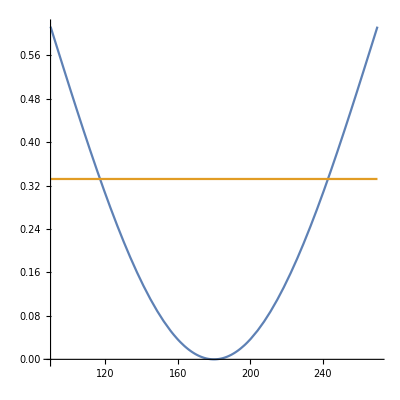

```mathematica
ParametricPlot[{{theta*180/Pi,U[theta]},{theta*180/Pi,E0}},{theta,Pi/2,3*Pi/2},AspectRatio->1]
```

## Problem 9.2

Write down equations for T and U for the same situation as in Problem 9.1. This time, however, make the following substitutions so that we can differentiate these functions with respect to time:
     in T change vtheta to R*theta’[t]
     in U change theta to theta[ t ]
Use dT / dt + dU / dt  = 0  to solve for theta[ t ].

```mathematica
Clear["`*"]
```

```mathematica
g=9.8;
m=0.125;
R=0.5;
vtheta0=2;
theta0=5*Pi/6;
```

```mathematica
T[t_]=m/2 * R^2 * theta'[t]^2;
U[t_]=m * g * R * (1 + Cos[theta[t]]);
```

### Solution

Note that you may get some long Mathematica error messages if your expressions for T and U are incorrect. They probably won't be of much help.

```mathematica
T$[t_]=m/2*R^2*(D[theta[t],t])^2;
U$[t_]=m*g*R*(1+Cos[theta[t]]);
If[FullSimplify[Solve[T$[t]==T[t],t]]=={{}},Print["T is correct."],Print["T is incorrect."]]
If[FullSimplify[Solve[U$[t]==U[t],t]]=={{}},Print["U is correct."],Print["U is incorrect."]]
```

T is correct.

U is correct.

Now solve the differential equation. Notice that the equation is a messy, nonlinear equation.

```mathematica
eqB=T'[t] + U'[t] == 0
sol=NDSolve[{eqB,theta[0]==theta0,theta'[0]==vtheta0},theta,{t,0,10}]
```

-0.6125 Sin[theta[t]] theta'[t]+0.03125 theta'[t] theta''[t]==0

{{theta→InterpolatingFunction[…]}}

Plot theta in degrees vs t. (Just execute this cell, no modifications necessary.)

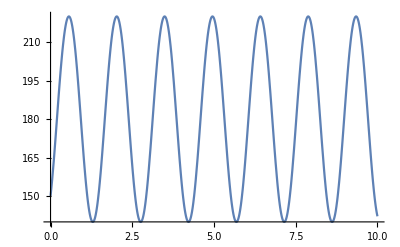

```mathematica
Plot[180/Pi*Evaluate[theta[t]/.sol],{t,0,10}]
```

```mathematica
x`
```

Do the classical turning points match the values from Problem 9.1? Describe the motion of the soap.

Input your response here.

## Written Problems